```mathematica
res我的几何分布=HypergeometricDistribution[5,6,10]  (*三个参数分别是: 一捧样本的容量=5, 总女数=6, 总男女人数=10*)
```

HypergeometricDistribution[5,6,10]

```mathematica
N[PDF[res我的几何分布,3]]  (*一捧中, 能获得3女的概率*)
```

0.47619

下面我们来看看, 这个”超几何分布”模型中, 
分别成功(即取到女的) 0次(人), 1次 , 2次, ..., 6次
 (因为总共只有6女, 所以最多也只能抽到6女) 的概率, 分别是多少?

```mathematica
res概率函数 = Table[PDF[res我的几何分布,i],{i,0,6}]
```

{0,1/42,5/21,10/21,5/21,1/42,0}

```mathematica
BarChart[res概率函数,LabelingFunction->Above]
```

(LabelingFunction→Above 这个参数, 
能在每条矩形上,上显示本条代表的数据值*)

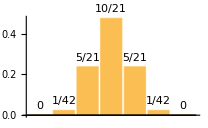

```mathematica
res累加函数 = Table[CDF[res我的几何分布,i],{i,0,6}]
```

{0,1/42,11/42,31/42,41/42,1,1}

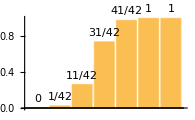

```mathematica
BarChart[res累加函数,LabelingFunction->Above]
```

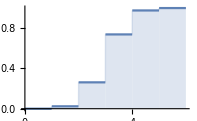

```mathematica
Plot[CDF[res我的几何分布,x],{x,0,6},Filling->Axis]
```

```mathematica
CDF[res我的几何分布,3] (*即上面的累加函数中,第3格的数字*)
```

能获得最多3女的概率 =  获得0女的概率 + 获得1女的概率
                                                             +获得2女的概率 + 获得3女的概率

31/42

```mathematica
N[31/42]
```

0.738095